#### CIE 1931 2-deg, XYZ CMFs

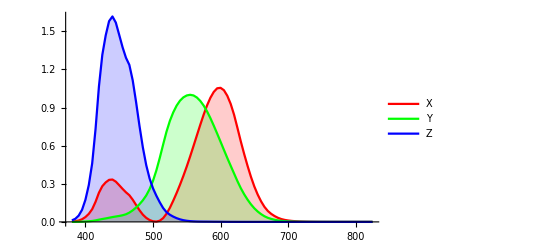

```mathematica
{λ,x,y,z}=Import["http://www.cvrl.org/database/data/cmfs/ciexyzjv.csv"]ᵀ;
ListLinePlot[{{λ,x}ᵀ,{λ,y}ᵀ,{λ,z}ᵀ},PlotLegends->{"X","Y","Z"},Filling->Axis,PlotStyle->{Red,Green,Blue}]
```

```mathematica
(* Color temperature in XYZ using Planck's radiation law.
See https://en.wikipedia.org/wiki/Planck%27s_law#Different_forms (wavelength). *)
```

```mathematica
λ=λ 10^-9;
XYZ[t_]:=Module[{h=6.62607*10^-34,c=2.998*10^8,k=1.38065*10^-23},{x,y,z}.((2 h c^2)/((-1+E^((h c/k)/(t λ))) λ^5))//#/#[[2]]&]
```

#### Color balance

```mathematica
(* xyY y coordinate from x coordinate for series D illuminants.
See https://en.wikipedia.org/wiki/Standard_illuminant#Illuminant_series_D *)
illuminant[x_]:=2.87*x-3*x^2-0.275

(* k = temperature, from -100 to +100, t = tint, from -100 to +100 *)
colorBalance[k_,t_]:=Module[
{x,y},
x=0.31271-k/100*If[k<0,0.214,0.066];
y=illuminant[x]+t/100*0.066;
XYZColor[x/y,1,(1-x-y)/y]
]
```

Temperature/tint vs Planckian locus

```mathematica
(* Reference chromaticity plot with sRGB gamut and D65 white point *)
p1=ChromaticityPlot[{"sRGB",Table[XYZColor@XYZ[i],{i,2000,50000,50}]},ImageSize->Large,Appearance->"VisibleSpectrum",PlotPoints->50,PlotTheme->"Marketing"];
```

```mathematica
(* Plot Planckian locus against chromaticity diagram. Also plots the position of the illuminant defined by a temperature and tint offset from D65. *)
Manipulate[
Show[p1,ChromaticityPlot[colorBalance[k,t],ImageSize->Large,PlotPoints->50,Appearance->None,PlotStyle->{Green,PointSize[0.01]}]
],
{{k,0},-100,100},{{t,0},-100,100}
]
```

Temperature scale factors

```mathematica
XYZ2xyY[xyz_]:={xyz[[1]]/(xyz[[1]]+xyz[[2]]+xyz[[3]]),xyz[[2]]/(xyz[[1]]+xyz[[2]]+xyz[[3]]),xyz[[2]]}
```

```mathematica
redFactor=Abs[XYZ2xyY[XYZ[2000]][[1]]-0.31271]
```

0.213976

```mathematica
blueFactor=Abs[XYZ2xyY[XYZ[50000]][[1]]-0.31271]
```

0.0655998